# SCIMATH301: Signals & Systems

## Group Project

## The Fast Fourier Transform: The Cooley-Tukey Algorithm

### Fall 2022

```mathematica
SetDirectory["directory"];
```

```mathematica
(*This clears all previously declared cariables, functions, and other vallues. *)
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
(*This is the implementation of the Cooley-Tukey Fast Fourier Transform. *)
FFT[signal_List ]:=If[

IntegerQ[Log2[Length[signal]]]==False,
Print["Error: The input signal must have a length that is a power of 2."],

If[


Length[signal]==1,
Return[signal],

Module[
{
xEven=FFT[Transpose[Partition[signal,2]][[1]]],
xOdd=FFT[Transpose[Partition[signal,2]][[2]]],
fourierTransform=ConstantArray[0,Length[signal]]
},

nSignal=Length[signal];
factor[k_]:=Exp[(-2π ⅉ)/nSignal*k];

For[i=1;k=0,i≤nSignal/2,i++;k++,
fourierTransform[[i]]=xEven[[i]]+factor[k]*xOdd[[i]];
fourierTransform[[i+nSignal/2]]=xEven[[i]]-factor[k]*xOdd[[i]]
];
Return[fourierTransform]
]
]
]
```

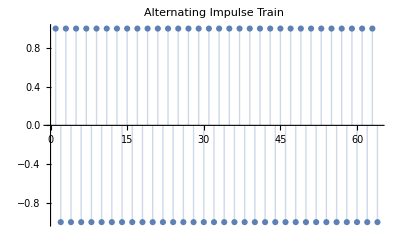

True

```mathematica
(*Here we ensure that the fourier transform works for an alternating impulse train *)
signal=RandomInteger[{1,1},2^6];
signal[[2;;;;2]]=-1;
ListPlot[signal,Filling->Axis,AxesLabel->Automatic,PlotLabel->"Alternating Impulse Train"]
Export["ImpulseTrain.png",Out[-1]];
FFT[signal]==Fourier[signal,FourierParameters->{1, -1}]
```

```mathematica
(*Here we try to see if the fourier transform works for alternating impulse trains of increasing lengths*)
(*We can see that the equivalence fails once the list becomes very large. But we can confirm below that the difference might be due to memory issues rather than a true loss of acuracy.*)
max=10;
signal=RandomInteger[{-10,10},2^max];
tests=Table[{2^n,FFT[signal[[;;2^n]]]==Fourier[ signal[[;;2^n]],FourierParameters->{1, -1}] },{n,0,max}];
Grid[tests,Frame->All]
```

1 | True
2 | True
4 | True
8 | True
16 | True
32 | True
64 | True
128 | False
256 | False
512 | False
1024 | False

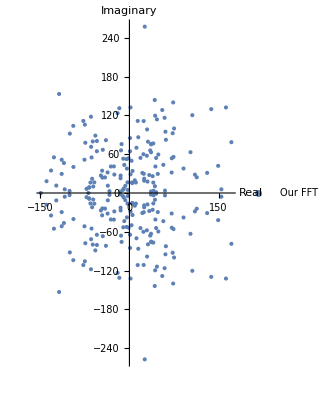

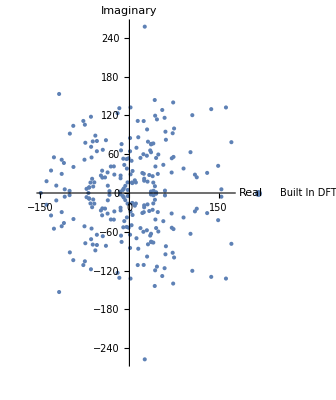

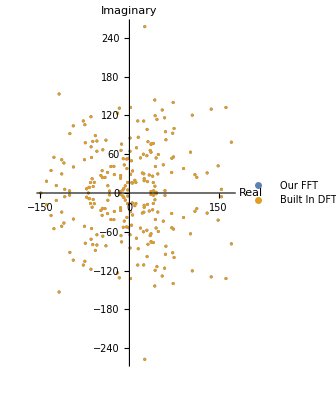

```mathematica
(*As we can see the dots still overlpap completely for large a large list size. *)
signal=RandomInteger[{-10,10},2^8];
ComplexListPlot[{FFT[signal]},PlotRange->Automatic,PlotLegends->{"Our FFT"},PlotLabels->Automatic, AxesLabel->{"Real","Imaginary"}]
ComplexListPlot[{Fourier[signal,FourierParameters->{1, -1}]},PlotRange->Automatic,PlotLegends->{"Built In DFT"},PlotLabels->Automatic, AxesLabel->{"Real","Imaginary"}]
ComplexListPlot[{FFT[signal],Fourier[signal,FourierParameters->{1, -1}]},PlotRange->Automatic,PlotLegends->{"Our FFT","Built In DFT"},PlotLabels->"",AxesLabel->{"Real","Imaginary"}]
```

```mathematica
(*Here we first investigate the time complexity of our algorithm by seeing how it performs with signals that are comprised of alternating impulse trains of varying lengths.*)
max=10;
signal=RandomInteger[{1,1},2^max];
signal[[2;;;;2]]=-1;
data=Table[
{
2^n,
First@AbsoluteTiming[FFT[signal[[;;2^n]]]],
First@AbsoluteTiming[Fourier[signal[[;;2^n]],FourierParameters->{1,-1}]]
},
{n,0,max}];
Grid[data,Frame->All]
```

1 | 0.000022 | 0.000063
2 | 0.000175 | 0.00002
4 | 0.00023 | 0.000015
8 | 0.000834 | 0.000031
16 | 0.001801 | 0.000031
32 | 0.003468 | 0.00003
64 | 0.006706 | 0.000029
128 | 0.019972 | 0.000057
256 | 0.05966 | 0.000059
512 | 0.144338 | 0.000101
1024 | 0.294765 | 0.000142

```mathematica
time1=data[[All,2]]
time2=data[[All,3]]
```

{0.000022,0.000175,0.00023,0.000834,0.001801,0.003468,0.006706,0.019972,0.05966,0.144338,0.294765}

{0.000063,0.00002,0.000015,0.000031,0.000031,0.00003,0.000029,0.000057,0.000059,0.000101,0.000142}

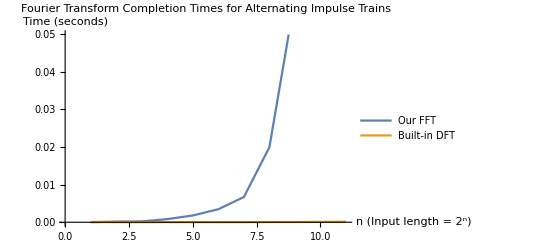

```mathematica
ListLinePlot[{time1,time2},PlotLegends->{"Our FFT","Built-in DFT"},PlotLabel->"Fourier Transform Completion Times for Alternating Impulse Trains",AxesLabel->{"n (Input length = 2^n)","Time (seconds)"}]
```

```mathematica
(*Secondly we investigate the time complexity of our algorithm by seeing how it performs with signals that are comprised of random real numbers between 0 and 5.*)
max=10;
signal=RandomReal[{0,5},2^max];
data=Table[
{
2^n,
First@AbsoluteTiming[FFT[signal[[;;2^n]]]],
First@AbsoluteTiming[Fourier[signal[[;;2^n]],FourierParameters->{1,-1}]]
},
{n,0,max}];
Grid[data,Frame->All]
```

1 | 0.000023 | 0.000034
2 | 0.000116 | 0.000013
4 | 0.000275 | 0.000016
8 | 0.000485 | 0.000014
16 | 0.001255 | 0.000016
32 | 0.002885 | 0.000029
64 | 0.006509 | 0.000037
128 | 0.016741 | 0.000055
256 | 0.037885 | 0.00006
512 | 0.080301 | 0.000081
1024 | 0.178168 | 0.000105

```mathematica
time1=data[[All,2]]
time2=data[[All,3]]
```

{0.000023,0.000116,0.000275,0.000485,0.001255,0.002885,0.006509,0.016741,0.037885,0.080301,0.178168}

{0.000034,0.000013,0.000016,0.000014,0.000016,0.000029,0.000037,0.000055,0.00006,0.000081,0.000105}

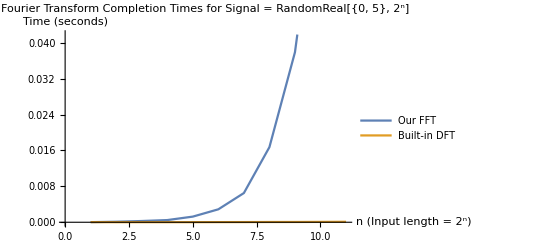

```mathematica
ListLinePlot[{time1,time2},PlotLegends->{"Our FFT","Built-in DFT"},PlotLabel->"Fourier Transform Completion Times for Signal = RandomReal[{0, 5}, 2^n]",AxesLabel->{"n (Input length = 2^n)","Time (seconds)"}]
```

```mathematica
(*Lastly we investigate the time complexity of our algorithm by seeing how it performs with more complicated signals that are comprised of random real numbers between -1000 and 1000.*)
max=10;
signal=RandomReal[{-1000,1000},2^max];
data=Table[
{
2^n,
First@AbsoluteTiming[FFT[signal[[;;2^n]]]],
First@AbsoluteTiming[Fourier[signal[[;;2^n]],FourierParameters->{1,-1}]]
},
{n,0,max}];
Grid[data,Frame->All]
```

1 | 0.000023 | 0.000037
2 | 0.000119 | 0.000013
4 | 0.00021 | 0.000013
8 | 0.000479 | 0.000013
16 | 0.001386 | 0.000022
32 | 0.003073 | 0.000026
64 | 0.007862 | 0.00003
128 | 0.016659 | 0.000044
256 | 0.044252 | 0.000075
512 | 0.082332 | 0.00007
1024 | 0.159784 | 0.000105

```mathematica
time1=data[[All,2]]
time2=data[[All,3]]
```

{0.000023,0.000119,0.00021,0.000479,0.001386,0.003073,0.007862,0.016659,0.044252,0.082332,0.159784}

{0.000037,0.000013,0.000013,0.000013,0.000022,0.000026,0.00003,0.000044,0.000075,0.00007,0.000105}

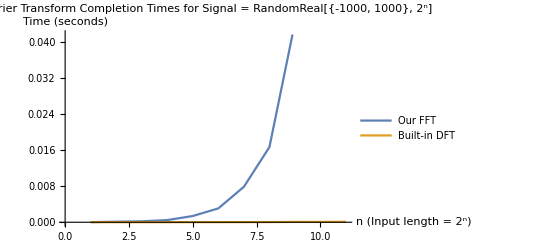

```mathematica
ListLinePlot[{time1,time2},PlotLegends->{"Our FFT","Built-in DFT"},PlotLabel->"Fourier Transform Completion Times for Signal = RandomReal[{-1000, 1000}, 2^n]",AxesLabel->{"n (Input length = 2^n)","Time (seconds)"}]
```